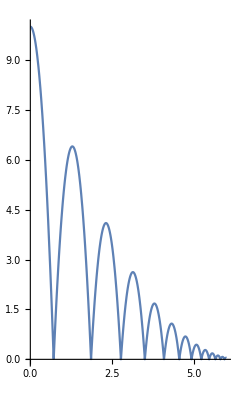

```mathematica
(* Исходные параметры *)
g  = 9.8;
y0 = 10;
v0x = 0.5;

(* Получение численного решения систем дифференциальных уравнений *)
ndsY = NDSolve[
{y''[t]==-g,y[0]==y0,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.8y'[t]]},
y,
{t,0,15}
];
ndsX = NDSolve[
{x''[t]== 0,x[0]==0,x'[0]==v0x},
x,
{t,0,15}
];

(* Построение графика *)
ParametricPlot[
Evaluate[{x[t], y[t]} /. Flatten@{ndsX, ndsY}], 
{t, 0, 12}
]
```